```mathematica
Quit
```

## Create the buttons at the top

```mathematica
Quit
```

```mathematica
With[{$pacletName="WeakCache", pid="JasonB"},
buttons=Row[{
Button["load "<>$pacletName<>" paclet",
$PublisherID;
$PublisherID=pid;
PacletDirectoryLoad[NotebookDirectory[]];
With[{syms=Join[Names[pid<>"`"<>$pacletName<>"`*"],Names[pid<>"`"<>$pacletName<>"`*`*"]]},(Unprotect[#];ClearAll[#];)&/@syms];
Get@(pid<>"`"<>$pacletName<>"`")
],
	Button["open resource definition notebook",NotebookOpen@FileNameJoin[{NotebookDirectory[],$pacletName,"ResourceDefinition.nb"}]
	]}
]];
SetOptions[EvaluationNotebook[],
DockedCells->Cell[BoxData[ToBoxes[buttons]],"DockedCell"]]
```

## Headline image

```mathematica
MoleculePlot[Molecule[…],ColorRules->{"C"->Directive[Black,Thick]},AtomLabels->None,Method->{"FontScaleFactor"->2}]
```

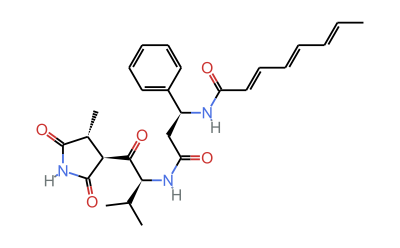
```mathematica
-Graphics-//shortInputForm
```

```mathematica
mplot=MoleculePlot[#,ColorRules->{("C"|"H")->Directive[Black,Thick],_->Directive[Red,Thick]},AtomLabels->None,Method->{"FontScaleFactor"->2},IncludeHydrogens->False]&;
SeedRandom[452];
WordCloud[Flatten[{1->ChemicalFormula["C14H24O2"],Thread[.99->mplot/@RandomSample[,17]]}],ImageSize->{325,275}]/.Tooltip->(#1&)
```

-Graphics-

```mathematica
mplot=MoleculePlot[#,ColorRules->{_->Directive[Black,Thick]},AtomLabels->None,Method->{"FontScaleFactor"->2}]&;
SeedRandom[45];
WordCloud[Flatten[{1->ChemicalFormula["C14H24O2"],Thread[.99->mplot/@RandomSample[,16]]}],ImageSize->{325,225}]/.Tooltip->(#1&)
```

```mathematica
SeedRandom[333];
mplot=MoleculePlot[#,ColorRules->{_->Directive[White,Thick]},AtomLabels->None]&
WordCloud[Flatten[{1->ChemicalFormula["C14H24O2"],Thread[.99->mplot/@RandomSample[,20]]}],ImageSize->{300,200},Background->Darker@Gray]/.Tooltip->(#1&)
```

MoleculePlot[#1,ColorRules→{_→Directive[White,Thick]},AtomLabels→None]&

-Graphics-

```mathematica
SeedRandom[1234];Rasterize[WordCloud[Flatten[{1->ChemicalFormula["C14H24O2"],Thread[.99->MoleculePlot/@RandomSample[,10]]}],ImageSize->300]]
```

-Graphics-

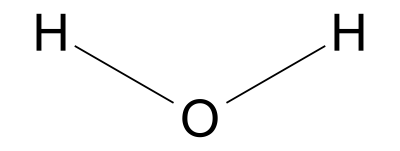

```mathematica
MoleculePlot["water",PlotTheme->"Monochrome"]
```

```mathematica
ImageIdentify[-Graphics-]
```

mathematical notation

## Tests

### Create tests

#### test writing function

```mathematica
Attributes[makeTest]={HoldRest};
makeTest[filename_,input_]:=With[{file=FileNameJoin[{NotebookDirectory[],"Tests",StringJoin[filename,If[StringEndsQ[filename,".mt"|".wlt"],"",".wlt"]]}]},
ResourceFunction["WriteUnitTest"][file,input]]
```

#### test-writing scratch

```mathematica
makeTest["TestCleanupAfter",Needs["JasonB`WeakCache`"]]
```

Adding test: TestCleanupAfter_20221024-YWV3YN

/Users/jasonb/WolframWorkspaces/Published_Paclets/WeakCache/Tests/TestCleanupAfter.wlt

```mathematica
makeTest["TestCleanupAfter",Block[{expr=Range[5],expr2=5},
CleanupAfter[expr,expr2 *=2];
{expr2,CompoundExpression[Unset[expr],expr2]}
]]
```

Adding test: TestCleanupAfter_20221024-TLXPW5

/Users/jasonb/WolframWorkspaces/Published_Paclets/WeakCache/Tests/TestCleanupAfter.wlt

```mathematica
makeTest["TestCleanupAfter",Block[{x},
{x=20,
Block[{expr=Range[5]},
CleanupAfter[expr,x *=2];
x
],
x}
]]
```

Adding test: TestCleanupAfter_20221024-TD3PHP

/Users/jasonb/WolframWorkspaces/Published_Paclets/WeakCache/Tests/TestCleanupAfter.wlt

### Run tests

```mathematica
condenseTestReport[tsr_MUnit`TestSuiteReportObject]:=TestReport@Evaluate@Replace[Normal@tsr@"Results",{_[file_,Failure[a_,b_Association]]:>Failure[a,Append[b,"TestFileName"->file]],_[file_,any_]:>any},{1}]
```

```mathematica
Block[{testdir=FileNameJoin[{NotebookDirectory[],"Tests"}],testfiles},
testfiles=FileNames["*.mt"|"*.wlt",testdir];
With[{pacletDir=NotebookDirectory[],files=testfiles},ResourceFunction["TestReportNotebook"]@condenseTestReport@PacletSymbol["MUnit","TestSuiteReport"][files,Initialization:>CompoundExpression[PacletDirectoryLoad[pacletDir]]]]
]
```

file$::shdw: Symbol file$ appears in multiple contexts {MUnit`Package`,Global`}; definitions in context MUnit`Package` may shadow or be shadowed by other definitions.

TestReportObject[…]

## Scratch